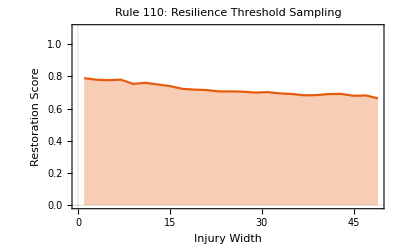

```mathematica
(*Resilience Sampling Function*)CalculateResilience[rule_,width_]:=Module[{steps=150,mixAt=50,init,clean,injured,diff,score},init=CenterArray[{1},301];
clean=CellularAutomaton[rule,init,steps];
(*Apply disruption at mixAt*)injured=Module[{pre,mid,post},pre=Take[clean,mixAt];
mid=Last[pre];
(*Random disruption of specified width*)mid[[151-width;;151+width]]=RandomInteger[1,2*width+1];
post=CellularAutomaton[rule,mid,steps-mixAt];
Join[pre,post]];
(*Difference Map XOR*)diff=MapThread[BitXor,{clean,injured},2];
(*Score:1.0=Perfect Healing;0.0=Total Failure*)score=1.0-(Total[Last[diff]]/Length[Last[diff]]);
score];

(*Sample Rule 110 across varying injury widths*)
samplingData=Table[{w,Mean[Table[CalculateResilience[110,w],{10}]]},{w,1,50,2}];

ListLinePlot[samplingData,PlotTheme->"Scientific",AxesLabel->{"Injury Width","Restoration Score"},PlotLabel->"Rule 110: Resilience Threshold Sampling",PlotRange->{0,1.1},Filling->Bottom]
```

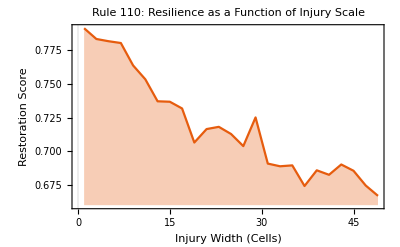

```mathematica
(*Function to calculate the percentage of recovery*)MeasureRecovery[rule_,injuryWidth_]:=Module[{steps=150,mixAt=50,init,clean,injured,diff},init=CenterArray[{1},301];
clean=CellularAutomaton[rule,init,steps];
(*Generate injured state*)injured=Module[{pre,mid,post},pre=Take[clean,mixAt];
mid=Last[pre];
(*Randomly perturb a section of width'injuryWidth'*)mid[[151-injuryWidth;;151+injuryWidth]]=RandomInteger[1,2*injuryWidth+1];
post=CellularAutomaton[rule,mid,steps-mixAt];
Join[pre,post]];
(*Calculate XOR Difference*)diff=MapThread[BitXor,{clean,injured},2];
(*Final row difference:1.0=Perfect recovery,0.0=Total divergence*)1.0-(Total[Last[diff]]/Length[Last[diff]])];

(*Run for Rule 110 across widths 1 to 50*)
data=Table[{w,Mean[Table[MeasureRecovery[110,w],{10}]]},{w,1,50,2}];
ListLinePlot[data,PlotTheme->"Scientific",AxesLabel->{"Injury Width (Cells)","Restoration Score"},PlotLabel->"Rule 110: Resilience as a Function of Injury Scale",Filling->Bottom]
```

```mathematica
(*Sweep all 256 rules for resilience to a 10-cell injury*)allRulesResilience=Table[{r,MeasureRecovery[r,5]},{r,0,255}];

(*Visualize the top 20 most resilient rules*)
topRules=TakeSortBy[allRulesResilience,Last,Greater][[{1;;20}]];
TableForm[topRules,TableHeadings->{None,{"Rule","Resilience Score"}}]
```

Part::pkspec1: The expression {1;;20} cannot be used as a part specification.

TakeSortBy[{{0,1.},{1,0.00332226},{2,0.986711},{3,0.0232558},{4,0.986711},{5,0.0199336},{6,0.976744},{7,0.00996678},{8,1.},{9,0.0531561},{10,0.980066},{11,0.0199336},{12,0.986711},{13,0.504983},{14,0.973422},{15,0.0299003},{16,0.986711},{17,0.0166113},{18,0.787375},{19,0.0232558},{20,0.980066},{21,0.0199336},{22,0.667774},{23,0.00664452},{24,0.990033},{25,0.0365449},{26,0.777409},{27,0.0332226},{28,0.990033},{29,0.0166113},{30,0.498339},{31,0.},{32,1.},{33,0.0265781},{34,0.983389},{35,0.0232558},{36,0.993355},{37,0.0398671},{38,0.976744},{39,0.0232558},{40,1.},{41,0.0299003},{42,0.980066},{43,0.0398671},{44,0.990033},{45,0.352159},{46,0.980066},{47,0.0299003},{48,0.983389},{49,0.0265781},{50,0.0166113},{51,0.0265781},{52,0.973422},{53,0.00664452},{54,0.352159},{55,0.0332226},{56,0.973422},{57,0.169435},{58,0.0166113},{59,0.0166113},{60,0.827243},{61,0.0498339},{62,0.33887},{63,0.0166113},{64,1.},{65,0.0332226},{66,0.986711},{67,0.0265781},{68,0.996678},{69,0.491694},{70,0.983389},{71,0.013289},{72,1.},{73,0.561462},{74,0.973422},{75,0.355482},{76,0.983389},{77,0.986711},{78,0.996678},{79,0.511628},{80,0.983389},{81,0.0199336},{82,0.79402},{83,0.0199336},{84,0.973422},{85,0.0232558},{86,0.475083},{87,0.00996678},{88,0.973422},{89,0.385382},{90,0.760797},{91,0.0332226},{92,0.973422},{93,0.508306},{94,0.956811},{95,0.0232558},{96,1.},{97,0.0963455},{98,0.980066},{99,0.169435},{100,0.986711},{101,0.372093},{102,0.807309},{103,0.0365449},{104,1.},{105,0.395349},{106,0.953488},{107,0.0564784},{108,0.976744},{109,0.541528},{110,0.757475},{111,0.0265781},{112,0.976744},{113,0.0299003},{114,0.00996678},{115,0.0299003},{116,0.980066},{117,0.0265781},{118,0.342193},{119,0.0232558},{120,0.936877},{121,0.0531561},{122,0.33887},{123,0.0265781},{124,0.774086},{125,0.0265781},{126,0.528239},{127,0.0332226},{128,1.},{129,0.694352},{130,0.983389},{131,0.345515},{132,0.993355},{133,0.956811},{134,0.9701},{135,0.508306},{136,1.},{137,0.787375},{138,0.983389},{139,0.973422},{140,0.996678},{141,0.990033},{142,0.966777},{143,0.980066},{144,0.986711},{145,0.342193},{146,0.727575},{147,0.501661},{148,0.983389},{149,0.531561},{150,0.647841},{151,0.833887},{152,0.986711},{153,0.853821},{154,0.744186},{155,0.986711},{156,0.966777},{157,0.986711},{158,0.265781},{159,0.986711},{160,1.},{161,0.774086},{162,0.980066},{163,0.0166113},{164,0.993355},{165,0.760797},{166,0.976744},{167,0.847176},{168,1.},{169,0.936877},{170,0.980066},{171,0.980066},{172,0.990033},{173,0.976744},{174,0.973422},{175,0.980066},{176,0.980066},{177,0.0365449},{178,0.0332226},{179,0.0166113},{180,0.9701},{181,0.857143},{182,0.767442},{183,0.920266},{184,0.966777},{185,0.9701},{186,0.0299003},{187,0.983389},{188,0.734219},{189,0.980066},{190,0.504983},{191,0.993355},{192,1.},{193,0.797342},{194,0.983389},{195,0.827243},{196,0.986711},{197,0.986711},{198,0.976744},{199,0.9701},{200,0.986711},{201,0.983389},{202,0.647841},{203,0.993355},{204,0.973422},{205,0.986711},{206,0.980066},{207,0.993355},{208,0.983389},{209,0.980066},{210,0.770764},{211,0.986711},{212,0.966777},{213,0.973422},{214,0.259136},{215,0.996678},{216,0.651163},{217,0.986711},{218,0.20598},{219,0.993355},{220,0.973422},{221,0.990033},{222,0.990033},{223,0.993355},{224,1.},{225,0.960133},{226,0.980066},{227,0.973422},{228,0.990033},{229,0.980066},{230,0.737542},{231,0.986711},{232,0.990033},{233,1.},{234,0.644518},{235,1.},{236,0.990033},{237,0.993355},{238,0.983389},{239,1.},{240,0.980066},{241,0.980066},{242,0.0232558},{243,0.990033},{244,0.973422},{245,0.976744},{246,0.501661},{247,0.990033},{248,0.627907},{249,1.},{250,0.345515},{251,1.},{252,0.980066},{253,1.},{254,0.993355},{255,1.}},Last,Greater]⟦{1;;20}⟧

```mathematica
(*Sweep all 256 rules for resilience to a 10-cell injury*)allRulesResilience=Table[{r,MeasureRecovery[r,5]},{r,0,255}];

(*Visualize the top 20 most resilient rules*)
topRules=TakeSortBy[allRulesResilience,Last,Greater][[{1;;20}]];
TableForm[topRules,TableHeadings->{None,{"Rule","Resilience Score"}}]
```

Part::pkspec1: The expression {1;;20} cannot be used as a part specification.

TakeSortBy[{{0,1.},{1,0.00332226},{2,0.990033},{3,0.00332226},{4,0.986711},{5,0.00996678},{6,0.983389},{7,0.},{8,1.},{9,0.0531561},{10,0.973422},{11,0.0265781},{12,0.990033},{13,0.495017},{14,0.960133},{15,0.0299003},{16,0.990033},{17,0.0232558},{18,0.787375},{19,0.00664452},{20,0.9701},{21,0.},{22,0.707641},{23,0.0365449},{24,0.983389},{25,0.0498339},{26,0.747508},{27,0.0232558},{28,0.966777},{29,0.0166113},{30,0.498339},{31,0.00996678},{32,1.},{33,0.0265781},{34,0.983389},{35,0.0232558},{36,0.993355},{37,0.0365449},{38,0.980066},{39,0.0232558},{40,1.},{41,0.0398671},{42,0.983389},{43,0.0199336},{44,0.986711},{45,0.372093},{46,0.973422},{47,0.0265781},{48,0.983389},{49,0.0265781},{50,0.0199336},{51,0.0199336},{52,0.980066},{53,0.0265781},{54,0.269103},{55,0.013289},{56,0.976744},{57,0.166113},{58,0.0199336},{59,0.0199336},{60,0.827243},{61,0.0365449},{62,0.33887},{63,0.0265781},{64,1.},{65,0.0664452},{66,0.983389},{67,0.0498339},{68,0.990033},{69,0.511628},{70,0.973422},{71,0.0232558},{72,1.},{73,0.551495},{74,0.980066},{75,0.358804},{76,0.986711},{77,0.993355},{78,0.973422},{79,0.495017},{80,0.983389},{81,0.0265781},{82,0.787375},{83,0.0332226},{84,0.973422},{85,0.0232558},{86,0.471761},{87,0.0166113},{88,0.976744},{89,0.375415},{90,0.734219},{91,0.0166113},{92,0.986711},{93,0.488372},{94,0.963455},{95,0.00664452},{96,1.},{97,0.0232558},{98,0.983389},{99,0.166113},{100,0.986711},{101,0.352159},{102,0.920266},{103,0.0431894},{104,1.},{105,0.395349},{106,0.980066},{107,0.0431894},{108,0.993355},{109,0.501661},{110,0.787375},{111,0.0365449},{112,0.976744},{113,0.0265781},{114,0.0199336},{115,0.0265781},{116,0.973422},{117,0.0265781},{118,0.33887},{119,0.0299003},{120,0.936877},{121,0.0332226},{122,0.348837},{123,0.0232558},{124,0.76412},{125,0.0431894},{126,0.79402},{127,0.013289},{128,1.},{129,0.747508},{130,0.983389},{131,0.33887},{132,0.990033},{133,0.953488},{134,0.986711},{135,0.511628},{136,1.},{137,0.780731},{138,0.983389},{139,0.980066},{140,0.983389},{141,0.986711},{142,0.966777},{143,0.966777},{144,0.990033},{145,0.352159},{146,0.800664},{147,0.528239},{148,0.980066},{149,0.504983},{150,0.641196},{151,0.677741},{152,0.980066},{153,0.827243},{154,0.787375},{155,0.983389},{156,0.963455},{157,0.986711},{158,0.262458},{159,0.996678},{160,1.},{161,0.740864},{162,0.980066},{163,0.0265781},{164,0.993355},{165,0.760797},{166,0.980066},{167,0.850498},{168,1.},{169,0.966777},{170,0.976744},{171,0.973422},{172,0.990033},{173,0.9701},{174,0.9701},{175,0.980066},{176,0.976744},{177,0.0365449},{178,0.00996678},{179,0.0166113},{180,0.980066},{181,0.847176},{182,0.687708},{183,0.920266},{184,0.980066},{185,0.973422},{186,0.0299003},{187,0.983389},{188,0.734219},{189,0.986711},{190,0.501661},{191,0.990033},{192,1.},{193,0.767442},{194,0.983389},{195,0.860465},{196,0.990033},{197,0.976744},{198,0.973422},{199,0.980066},{200,0.990033},{201,0.983389},{202,0.983389},{203,0.990033},{204,0.990033},{205,0.9701},{206,0.983389},{207,0.996678},{208,0.980066},{209,0.980066},{210,0.79402},{211,0.986711},{212,0.980066},{213,0.966777},{214,0.418605},{215,0.980066},{216,0.986711},{217,0.990033},{218,0.212625},{219,0.990033},{220,0.976744},{221,0.986711},{222,0.990033},{223,0.986711},{224,1.},{225,0.960133},{226,0.9701},{227,0.9701},{228,0.990033},{229,0.980066},{230,0.750831},{231,0.986711},{232,0.986711},{233,0.993355},{234,0.644518},{235,1.},{236,0.980066},{237,1.},{238,0.980066},{239,1.},{240,0.973422},{241,0.980066},{242,0.0299003},{243,0.986711},{244,0.973422},{245,0.980066},{246,0.498339},{247,0.990033},{248,0.651163},{249,1.},{250,0.335548},{251,1.},{252,0.980066},{253,1.},{254,0.993355},{255,1.}},Last,Greater]⟦{1;;20}⟧

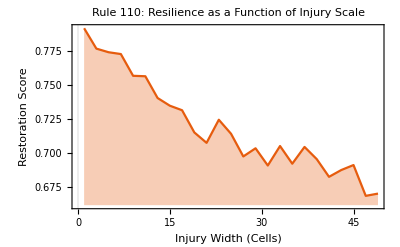

```mathematica
(*Function to calculate the percentage of recovery*)MeasureRecovery[rule_,injuryWidth_]:=Module[{steps=150,mixAt=50,init,clean,injured,diff},init=CenterArray[{1},301];
clean=CellularAutomaton[rule,init,steps];
(*Generate injured state*)injured=Module[{pre,mid,post},pre=Take[clean,mixAt];
mid=Last[pre];
(*Randomly perturb a section of width'injuryWidth'*)mid[[151-injuryWidth;;151+injuryWidth]]=RandomInteger[1,2*injuryWidth+1];
post=CellularAutomaton[rule,mid,steps-mixAt];
Join[pre,post]];
(*Calculate XOR Difference*)diff=MapThread[BitXor,{clean,injured},2];
(*Final row difference:1.0=Perfect recovery,0.0=Total divergence*)1.0-(Total[Last[diff]]/Length[Last[diff]])];

(*Run for Rule 110 across widths 1 to 50*)
data=Table[{w,Mean[Table[MeasureRecovery[110,w],{10}]]},{w,1,50,2}];
ListLinePlot[data,PlotTheme->"Scientific",AxesLabel->{"Injury Width (Cells)","Restoration Score"},PlotLabel->"Rule 110: Resilience as a Function of Injury Scale",Filling->Bottom]
```

```mathematica
(*Sweep all 256 rules for resilience to a 10-cell injury*)allRulesResilience=Table[{r,MeasureRecovery[r,5]},{r,0,255}];

(*Visualize the top 20 most resilient rules*)
topRules=TakeSortBy[allRulesResilience,Last,Greater][[{1;;20}]];
TableForm[topRules,TableHeadings->{None,{"Rule","Resilience Score"}}]
```

Part::pkspec1: The expression {1;;20} cannot be used as a part specification.

TakeSortBy[{{0,1.},{1,0.00332226},{2,0.983389},{3,0.00996678},{4,0.993355},{5,0.013289},{6,0.9701},{7,0.},{8,1.},{9,0.0498339},{10,0.983389},{11,0.0265781},{12,0.990033},{13,0.511628},{14,0.980066},{15,0.0232558},{16,0.986711},{17,0.0199336},{18,0.813953},{19,0.013289},{20,0.9701},{21,0.},{22,0.66113},{23,0.00996678},{24,0.983389},{25,0.0498339},{26,0.797342},{27,0.0199336},{28,0.976744},{29,0.00996678},{30,0.51495},{31,0.00664452},{32,1.},{33,0.0232558},{34,0.983389},{35,0.00996678},{36,0.996678},{37,0.013289},{38,0.976744},{39,0.0299003},{40,1.},{41,0.0332226},{42,0.980066},{43,0.0299003},{44,0.986711},{45,0.372093},{46,0.980066},{47,0.0232558},{48,0.993355},{49,0.0332226},{50,0.0199336},{51,0.0199336},{52,0.986711},{53,0.0232558},{54,0.345515},{55,0.013289},{56,0.980066},{57,0.166113},{58,0.0199336},{59,0.0166113},{60,0.873754},{61,0.0365449},{62,0.33887},{63,0.013289},{64,1.},{65,0.0697674},{66,0.983389},{67,0.0398671},{68,0.996678},{69,0.504983},{70,0.980066},{71,0.0199336},{72,1.},{73,0.578073},{74,0.983389},{75,0.368771},{76,0.980066},{77,0.973422},{78,0.976744},{79,0.488372},{80,0.980066},{81,0.0265781},{82,0.744186},{83,0.0166113},{84,0.973422},{85,0.0199336},{86,0.504983},{87,0.},{88,0.983389},{89,0.365449},{90,0.734219},{91,0.0431894},{92,0.976744},{93,0.511628},{94,0.950166},{95,0.013289},{96,1.},{97,0.0365449},{98,0.980066},{99,0.166113},{100,0.990033},{101,0.385382},{102,0.86711},{103,0.0498339},{104,0.993355},{105,0.398671},{106,0.950166},{107,0.0730897},{108,0.990033},{109,0.551495},{110,0.79402},{111,0.0431894},{112,0.973422},{113,0.0265781},{114,0.0265781},{115,0.013289},{116,0.986711},{117,0.0199336},{118,0.33887},{119,0.0199336},{120,0.950166},{121,0.0232558},{122,0.345515},{123,0.0166113},{124,0.770764},{125,0.0398671},{126,0.79402},{127,0.0365449},{128,1.},{129,0.79402},{130,0.986711},{131,0.33887},{132,0.986711},{133,0.966777},{134,0.980066},{135,0.491694},{136,1.},{137,0.770764},{138,0.973422},{139,0.966777},{140,0.990033},{141,0.986711},{142,0.966777},{143,0.973422},{144,0.983389},{145,0.358804},{146,0.760797},{147,0.501661},{148,0.980066},{149,0.51495},{150,0.654485},{151,0.760797},{152,0.983389},{153,0.860465},{154,0.777409},{155,0.976744},{156,0.993355},{157,0.993355},{158,0.594684},{159,0.990033},{160,1.},{161,0.687708},{162,0.983389},{163,0.0166113},{164,0.996678},{165,0.760797},{166,0.980066},{167,0.857143},{168,1.},{169,0.900332},{170,0.983389},{171,0.973422},{172,0.990033},{173,0.973422},{174,0.980066},{175,0.983389},{176,0.976744},{177,0.0265781},{178,0.0265781},{179,0.00664452},{180,0.973422},{181,0.767442},{182,0.674419},{183,0.946844},{184,0.973422},{185,0.976744},{186,0.0265781},{187,0.986711},{188,0.737542},{189,0.983389},{190,0.511628},{191,0.993355},{192,1.},{193,0.760797},{194,0.986711},{195,0.833887},{196,0.990033},{197,0.966777},{198,0.980066},{199,0.990033},{200,0.990033},{201,0.976744},{202,0.986711},{203,0.990033},{204,0.980066},{205,0.983389},{206,0.976744},{207,0.986711},{208,0.980066},{209,0.980066},{210,0.760797},{211,0.983389},{212,0.980066},{213,0.973422},{214,0.262458},{215,0.980066},{216,0.647841},{217,0.990033},{218,0.199336},{219,0.993355},{220,0.980066},{221,0.990033},{222,0.983389},{223,0.986711},{224,1.},{225,0.906977},{226,0.966777},{227,0.9701},{228,0.993355},{229,0.980066},{230,0.734219},{231,0.986711},{232,0.990033},{233,1.},{234,0.631229},{235,1.},{236,0.9701},{237,1.},{238,0.980066},{239,1.},{240,0.966777},{241,0.983389},{242,0.0166113},{243,0.983389},{244,0.956811},{245,0.976744},{246,0.501661},{247,0.996678},{248,0.647841},{249,1.},{250,0.33887},{251,1.},{252,0.980066},{253,1.},{254,0.993355},{255,1.}},Last,Greater]⟦{1;;20}⟧

```mathematica
(*1. Setup Parameters*)rule=30; (*The rule we are studying*)
steps1=50; (*Initial evolution time*)
steps2=100; (*Time after mixing*)
perturbWidth=20; (*How many cells to'mix up'*)
(*2. Run the initial evolution*)
init=CenterArray[{1},201];
evolution1=CellularAutomaton[rule,init,steps1];
latestState=Last[evolution1];
(*3. Mix up the latest cells*)
(*We replace a central block with random 0s and 1s*)
mid=IntegerPart[Length[latestState]/2];
perturbedState=latestState;
perturbedState⟦mid-perturbWidth;;mid+perturbWidth⟧=RandomInteger[1,2*perturbWidth+1];
(*4. Run the recovery evolution*)
evolution2=CellularAutomaton[rule,perturbedState,steps2];
(*5. Visualize the result*)
ArrayPlot[Join[evolution1,evolution2],Mesh->True,ColorRules->{0->White,1->Black},Epilog->{Red,Thickness[0.005],Line[{{0,steps2+steps1-steps1},{201,steps2+steps1-steps1}}]},PlotLabel->"Pattern Restoration Experiment (Red Line = Mixing Point)"]
```

-Graphics-

```mathematica
-Graphics-(*1. Setup Parameters*)rule=30;
steps1=50;
steps2=100;
perturbWidth=20;

(*2. Initial evolution (Common to both)*)
init=CenterArray[{1},201];
evolution1=CellularAutomaton[rule,init,steps1];
latestState=Last[evolution1];

(*3. Branching:Control vs Perturbed*)
(*Control:No changes*)
controlEvolution2=CellularAutomaton[rule,latestState,steps2];

(*Perturbed:Mix up the central cells*)
mid=IntegerPart[Length[latestState]/2];
perturbedState=latestState;
perturbedState[[mid-perturbWidth;;mid+perturbWidth]]=RandomInteger[1,2*perturbWidth+1];
experimentEvolution2=CellularAutomaton[rule,perturbedState,steps2];

(*4. Visualization*)
controlPlot=ArrayPlot[Join[evolution1,controlEvolution2],ColorRules->{0->White,1->Black},PlotLabel->"Control (No Injury)"];

experimentPlot=ArrayPlot[Join[evolution1,experimentEvolution2],ColorRules->{0->White,1->Black},Epilog->{Red,Thickness[0.01],Line[{{0,steps2+steps1-steps1},{201,steps2+steps1-steps1}}]},PlotLabel->"Experiment (With Injury)"];

GraphicsGrid[{{controlPlot,experimentPlot}},ImageSize->Large]
```

Set::write: Tag Times in … is Protected.

-Graphics-

```mathematica
(*1. Setup Parameters*)rule=30; (*The rule under study[cite:1,5,207]*)
steps1=50; (*Initial evolution time[cite:3,6,210]*)
steps2=100; (*Time after mixing[cite:4,6,211]*)
perturbWidth=20; (*Width of the'mixed' region[cite:6,212]*)
(*2. Initial Evolution*)
init=CenterArray[{1},201];[cite:8,214]
evolution1=CellularAutomaton[rule,init,steps1];[cite:9,215]
latestState=Last[evolution1];[cite:10,216]
(*3. Mixing/Perturbation*)
mid=IntegerPart[Length[latestState]/2];[cite:13,218]
perturbedState=latestState;[cite:14,219]
(*Corrected syntax for part assignment[cite:220]*)
perturbedState⟦mid-perturbWidth;;mid+perturbWidth⟧=RandomInteger[1,2*perturbWidth+1];[cite:15,221]
(*4. Recovery Evolution*)
evolution2=CellularAutomaton[rule,perturbedState,steps2];[cite:17,223]
(*5. Visualization*)
ArrayPlot[Join[evolution1,evolution2],Mesh->True,ColorRules->{0->White,1->Black},[cite:19,20,225,226] Epilog->{Red,Thickness[0.005],Line[{{0,steps1},{201,steps1}}]},(*Fixed coordinate to the mixing point[cite:226]*)PlotLabel->"Pattern Restoration Experiment (Red Line = Mixing Point)"][cite:21,227]
```

Null[cite:8,214]

Null[cite:9,215]

Null[cite:10,216]

Null[cite:13,218]

Null[cite:14,219]

Null[cite:15,221]

Null[cite:17,223]

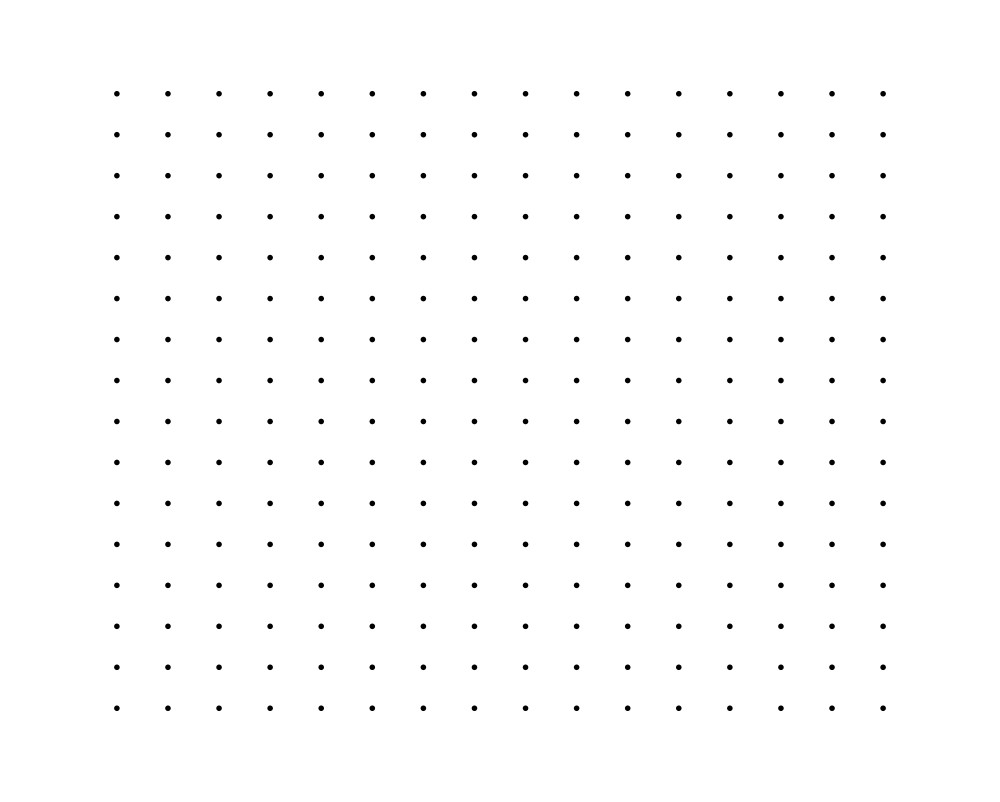

```mathematica
(*Ruliological Sweep of All 256 Rules*)stepsBefore=100;
stepsAfter=50;
width=201;
results=Table[Module[{init,clean,mixed,diff,midRow,perturbWidth=10},init=CenterArray[{1},width];
(*1. The'Clean' Path*)clean=CellularAutomaton[rule,init,stepsBefore+stepsAfter];
(*2. The'Mixed' Path (Interrupt at Row 100)*)midState=clean⟦stepsBefore+1⟧;
(*Randomize a section of the row*)perturbedState=ReplacePart[midState,Thread[Range[101-perturbWidth,101+perturbWidth]->RandomInteger[1,2 perturbWidth+1]]];
mixed=Join[Take[clean,stepsBefore],CellularAutomaton[rule,perturbedState,stepsAfter]];
(*3. The Difference Map (XOR)*)diff=MapThread[BitXor,{clean,mixed},2];
(*Return a small plot for each rule*)ArrayPlot[diff,ColorRules->{1->Red,0->White},Frame->False,PlotLabel->Style[rule,8]]],{rule,0,255}];
(*Display as a 16x16 grid*)
GraphicsGrid[Partition[results,16],ImageSize->1000]
```

```mathematica
(*1. Setup Parameters*)rule=30; (*The rule under study[cite:1,5,207]*)
steps1=50; (*Initial evolution time[cite:3,6,210]*)
steps2=100; (*Time after mixing[cite:4,6,211]*)
perturbWidth=20; (*Width of the'mixed' region[cite:6,212]*)
(*2. Initial Evolution*)
init=CenterArray[{1},201];[cite:8,214]
evolution1=CellularAutomaton[rule,init,steps1];[cite:9,215]
latestState=Last[evolution1];[cite:10,216]
(*3. Mixing/Perturbation*)
mid=IntegerPart[Length[latestState]/2];[cite:13,218]
perturbedState=latestState;[cite:14,219]
(*Corrected syntax for part assignment[cite:220]*)
perturbedState⟦mid-perturbWidth;;mid+perturbWidth⟧=RandomInteger[1,2*perturbWidth+1];[cite:15,221]
(*4. Recovery Evolution*)
evolution2=CellularAutomaton[rule,perturbedState,steps2];[cite:17,223]
(*5. Visualization*)
ArrayPlot[Join[evolution1,evolution2],Mesh->True,ColorRules->{0->White,1->Black},[cite:19,20,225,226] Epilog->{Red,Thickness[0.005],Line[{{0,steps1},{201,steps1}}]},(*Fixed coordinate to the mixing point[cite:226]*)PlotLabel->"Pattern Restoration Experiment (Red Line = Mixing Point)"][cite:21,227]
```

Null[cite:8,214]

Null[cite:9,215]

Null[cite:10,216]

Null[cite:13,218]

Null[cite:14,219]

Null[cite:15,221]

Null[cite:17,223]

```mathematica
(*Define Parameters*)ruleNumber=110;steps=200;gridSize=200;noiseProb=0.02;

(*Initial State:Single Seed*)initialState=CenterArray[1,gridSize];

(*Function to evolve with noise*)evolveWithNoise[state_,rule_]:=Module[{nextState,noiseMask},nextState=CellularAutomaton[rule,state,1][[2]];noiseMask=RandomChoice[{1-noiseProb,noiseProb}->{0,1},gridSize];BitXor[nextState,noiseMask]];

(*Run the simulation*)stochasticEvolution=NestList[evolveWithNoise[#,ruleNumber]&,initialState,steps];

(*Visualize Results*)ArrayPlot[stochasticEvolution,ColorRules->{0->White,1->Black},Mesh->False,Frame->True,FrameLabel->{"Cell Index","Time Step"},PlotLabel->"Rule "<>ToString[ruleNumber]<>" with "<>ToString[noiseProb*100]<>"% Continuous Noise"]
```

-Graphics-

```mathematica
(*Parameters*)rule=110;steps=200;gridSizes={50,100,200,500};injuryWidth=10;injuryTime=50;

(*Function to calculate restoration for a specific size) testSize[L_]:=Module[{control,injury,diff},(Control Evolution*)control=CellularAutomaton[rule,CenterArray[1,L],steps];

(*Create Injury at injuryTime*)injuredState=control[[injuryTime+1]];mid=Floor[L/2];injuredState[[mid-Floor[injuryWidth/2];;mid+Floor[injuryWidth/2]]]=RandomInteger[{0,1},injuryWidth+1];

(*Evolve Injury*)injury=CellularAutomaton[rule,injuredState,steps-injuryTime];

(*Compare only the steps after injury*)diff=Total[BitXor[control[[injuryTime+1;;]],injury],2];

(*Return 1 if healed (diff is 0),0 otherwise*)If[diff==0,1,0]];

(*Run the loop and print results*)results=Table[{s,testSize[s]},{s,gridSizes}];Print["Grid Size vs Healing Success (1=Healed, 0=Failed): ",results]
```

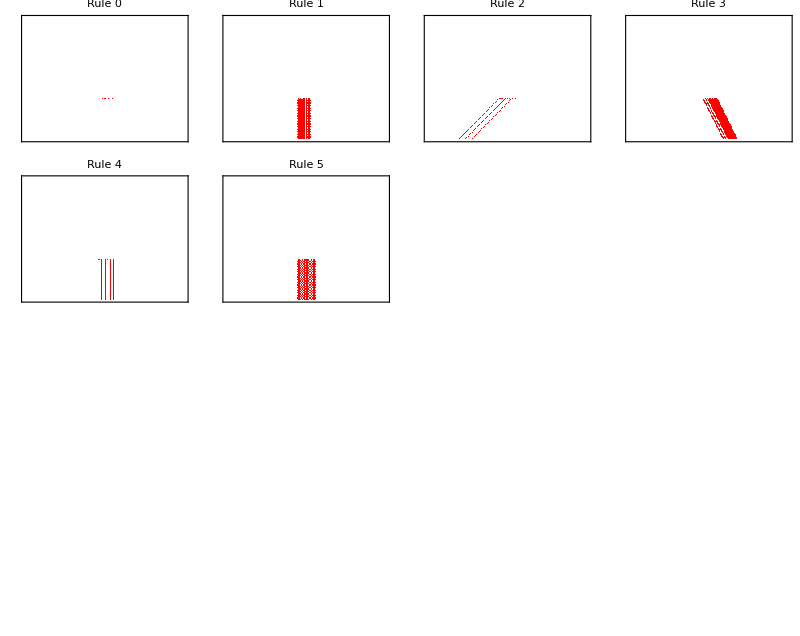

```mathematica
(*Parameters*)stepsBefore=100;
stepsAfter=50;
width=201;
perturbWidth=10;

(*Function to generate a single rule plot*)
generateRulePlot[rule_]:=Module[{init,clean,midState,perturbedState,mixed,diff},init=CenterArray[{1},width];
clean=CellularAutomaton[rule,init,stepsBefore+stepsAfter];
midState=clean[[stepsBefore+1]];
perturbedState=ReplacePart[midState,Thread[Range[101-perturbWidth,101+perturbWidth]->RandomInteger[1,2 perturbWidth+1]]];
mixed=Join[Take[clean,stepsBefore],CellularAutomaton[rule,perturbedState,stepsAfter]];
diff=MapThread[BitXor,{clean,mixed},2];
ArrayPlot[diff,ColorRules->{1->Red,0->White},Frame->True,FrameTicks->None,PlotLabel->Style["Rule "<>ToString[rule],10]]];

(*Generate all 256 plots*)
allPlots=Table[generateRulePlot[r],{r,0,255}];

(*Partition into 16 groups (16 rules each)*)
figureGroups=Partition[allPlots,16];

(*Display the first group (Rules 0-15) as an example*)
(*To export all 16,you would loop this or use Export[]*)
GraphicsGrid[Partition[figureGroups[[1]],4],ImageSize->800,Spacings->10]
```

```mathematica
(*1. Setup Directories*)exportFolder=FileNameJoin[{$HomeDirectory,"Desktop","Individual_Rule_Panels"}];
If[!FileExistsQ[exportFolder],CreateDirectory[exportFolder]];

(*2. Parameters*)
stepsBefore=100;
stepsAfter=50;
width=201;
perturbWidth=10;

(*3. Generation and Export Loop*)
Do[Module[{init,clean,midState,perturbedState,mixed,diff,plot,fileName},(*Generate original CA evolution*)init=CenterArray[{1},width];
clean=CellularAutomaton[rule,init,stepsBefore+stepsAfter];
(*Capture state at the perturbation point*)midState=clean[[stepsBefore+1]];
(*Create perturbed state by flipping bits in the center*)perturbedState=ReplacePart[midState,Thread[Range[101-perturbWidth,101+perturbWidth]->RandomInteger[1,2 perturbWidth+1]]];
(*Generate evolution from the perturbed state*)mixed=Join[Take[clean,stepsBefore],CellularAutomaton[rule,perturbedState,stepsAfter]];
(*Calculate the Difference Map (XOR) to isolate the error cone*)diff=MapThread[BitXor,{clean,mixed},2];
(*Create the individual plot for this rule*)plot=ArrayPlot[diff,ColorRules->{1->Red,0->White},Frame->True,FrameTicks->None,ImageSize->400,PlotLabel->Style["Rule "<>ToString[rule],14,Bold]];
(*Export as a singular PNG for this specific rule*)(*IntegerString with 10,3 ensures files are named Rule_000.png,Rule_001.png,etc.*)fileName=FileNameJoin[{exportFolder,"Rule_"<>IntegerString[rule,10,3]<>".png"}];
Export[fileName,plot,"PNG"];
(*Progress tracking*)If[Mod[rule,32]==0,Print["Processing Rule: ",rule]];],{rule,0,255}];

Print["Done! 256 individual panels have been saved to the 'Individual_Rule_Panels' folder on your Desktop."];
```

Processing Rule: 0

Processing Rule: 32

Processing Rule: 64

Processing Rule: 96

Processing Rule: 128

Processing Rule: 160

Processing Rule: 192

Processing Rule: 224

Done! 256 individual panels have been saved to the 'Individual_Rule_Panels' folder on your Desktop.

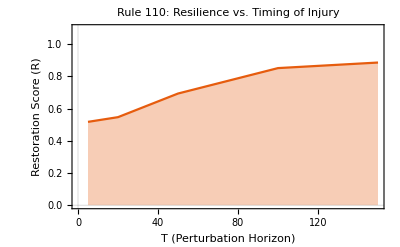

```mathematica
(*Parameters*)rule=110;
gridSize=301;
steps=300;
injuryWidth=10;
tHorizons={5,20,50,100,150}; (*Testing different T values*)

(*Reuse the CalculateResilience logic but make T a variable*)
testTIndependence[rule_,t_]:=Module[{init,clean,injured,diff,score},init=CenterArray[1,gridSize];
clean=CellularAutomaton[rule,init,steps];
(*Apply disruption at time T*)mid=clean[[t+1]];
mid[[Floor[gridSize/2]-injuryWidth;;Floor[gridSize/2]+injuryWidth]]=RandomInteger[1,2*injuryWidth+1];
(*Evolve injured state for the remaining steps*)post=CellularAutomaton[rule,mid,steps-t];
injured=Join[Take[clean,t],post];
(*Difference Map and Score*)diff=MapThread[BitXor,{clean,injured},2];
score=1.0-(Total[Last[diff]]/gridSize);
score];

(*Run Sampling*)
tData=Table[{t,Mean[Table[testTIndependence[rule,t],{10}]]},{t,tHorizons}];

(*Visualize results*)
ListLinePlot[tData,PlotTheme->"Scientific",AxesLabel->{"T (Perturbation Horizon)","Restoration Score (R)"},PlotLabel->"Rule "<>ToString[rule]<>": Resilience vs. Timing of Injury",PlotRange->{0,1.1},Filling->Bottom]
```